```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210507_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
stoichioforhomosapiens=Drop[Import["../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

understanding the FBA model work principles

```mathematica
boundaries=RandomChoice[{0.1,0.9}->{{-5,5},{-500,500}},fluxexchanges];
```

```mathematica
Dimensions@boundaries
```

{1008,2}

```mathematica
subsetsizechoice=RandomInteger[{1,fluxexchanges}]
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
```

218

```mathematica
Dimensions@subsetpositions
```

{218}

```mathematica
coefficients=Table[RandomReal[{-2,2},subsetsizechoice],sequencesize=300];
Dimensions@coefficients
```

{300,218}

```mathematica
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}];
Dimensions@objectivefunctions
```

{300,1008}

```mathematica
solutionvectors=Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}];
```

```mathematica
Dimensions@boundaries
Dimensions@objectivefunctions
Dimensions@solutionvectors
```

{1008,2}

{300,1008}

{300,1008}

```mathematica
Position[boundaries,_?(#≠{-500,500}&)];
```

```mathematica
Position[solutionvectors[[1]],_?(Abs@#<5&)];
```

```mathematica
Length @Cases[stoichiometricmatrix.solutionvectors[[1]],_?(Abs@#<10^(-5)&)]
```

738

```mathematica
MapThread[Dot,{objectivefunctions,solutionvectors}][[{1,2,3}]]
```

{60645.5,61757.8,66689.5}

```mathematica
objectivefunctions[[1]].solutionvectors[[1]]
boundaries[[1]]
objectivefunctions[[1]];
solutionvectors[[1]]
```

60645.5

{-500,500}

{411.808,88.192,88.192,-309.54,-221.348,500.,278.652,278.652,500.,251.758,1.1082×10^-6,58.5749,-500.,500.,500.,5.,-4.45757×10^-7,500.,500.,500.,-4.45746×10^-7,-207.327,500.,-500.,-292.673,-207.327,-207.327,25.2985,-4.45761×10^-7,1.4163×10^-6,9.70505×10^-7,-500.,-500.,-500.,-500.,-182.029,187.029,209.311,5.,500.,5.,-245.994,-500.,250.994,100.605,-399.395,500.,500.,500.,-108.707,500.,-249.006,-249.006,-249.006,-399.395,496.104,173.854,500.,-30.4101,5.,-500.,-322.25,496.104,496.104,3.89617,-318.743,181.257,500.,500.,-495.,-500.,-500.,5.,-500.,5.,5.,-500.,1.24562×10^-7,500.,1.55226×10^-8,500.,500.,500.,500.,-500.,-318.324,-500.,489.099,157.094,0.901267,181.676,0.419939,-500.,0.481328,0.481328,-500.,0.481328,-167.094,-500.,490.,88.192,500.,500.,500.,-262.782,-257.782,-242.218,5.75767×10^-10,-500.,-500.,500.,291.765,15.,111.727,500.,500.,-208.235,1.73039×10^-7,111.727,500.,-208.235,111.727,-208.235,-500.,-500.,-500.,-500.,500.,-5.89285×10^-7,15.,15.,5.,4.94953,-0.0504689,500.,500.,-5.89289×10^-7,-5.89296×10^-7,-0.0319354,-0.031936,5.,79.2417,5.,485.,-5.,7.1049×10^-8,79.2097,79.2097,-5.,0.0178408,117.071,-500.,-500.,1.64758×10^-7,-495.,500.,-500.,-500.,-500.,-201.281,-500.,-500.,-350.605,149.395,-32.3616,181.757,181.757,-5.,-0.0790054,-162.91,-162.831,181.757,500.,-0.0790054,-500.,-0.0790054,-350.605,113.105,-99.6604,5.,-212.765,113.105,-125.846,-125.925,130.925,5.,5.,-160.524,113.105,386.895,500.,-4.68757×10^-6,-182.904,-339.476,5.,-344.476,5.,-322.096,5.,-500.,-0.0284516,5.,5.,-162.884,-121.745,-162.856,-0.0284516,-0.0284516,187.12,-86.5152,100.605,251.895,248.105,-10.,500.,-345.605,5.,500.,4.94881,154.395,207.288,37.7116,-500.,-0.0511861,245.,5.,5.,5.,500.,500.,208.235,500.,-5.,9.28795×10^-8,5.,-192.226,-5.,500.,5.,-500.,-149.11,167.011,500.,-5.,1.54×10^-7,1.53996×10^-7,-321.121,-500.,-5.,-0.00757184,-500.,500.,1.53995×10^-7,-134.967,5.,-496.345,-253.606,-2.80896×10^-7,7.69936×10^-8,7.70044×10^-8,10.,500.,-500.,-1.51318×10^-7,2.80894×10^-7,-500.,312.774,372.869,-500.,-2.10159×10^-8,-5.,-5.,495.,127.131,500.,5.,500.,-32.2497,-10.,500.,5.,5.,-162.87,-500.,430.807,-81.3276,500.,5.,5.,7.70015×10^-8,5.,-452.824,-500.,442.824,496.896,413.672,0.625,3.10379,500.,0.625,2.09938×10^-8,15.8533,180.06,-5.,69.2665,500.,-265.179,-500.,5.,-5.,391.966,-125.88,15.1898,-6.00664×10^-9,-4.89625×10^-8,-364.12,15.1898,5.,-7.61416×10^-8,5.,-500.,-5.,500.,5.,5.,-500.,-500.,-5.,500.,-500.,-500.,2.17138×10^-7,-2.17136×10^-7,181.948,-500.,-318.052,500.,353.43,0.251399,65.6595,500.,5.,5.,413.485,278.724,86.5152,81.5152,5.,-5.,-500.,-500.,-500.,5.,-15.,5.,5.,0.625,1.13173×10^-8,-500.,-5.,-5.,500.,-500.,5.,-500.,-500.,500.,-199.301,-500.,-300.699,-300.702,3.02246×10^-8,500.,500.,495.,0.00298801,-500.,5.,2.5,-85.6925,500.,5.,0.00298801,-490.,-5.,-5.,-5.,5.,-500.,205.424,-127.954,0.00298801,-5.,333.378,500.,0.625,349.124,4.375,-500.,205.424,349.124,205.424,500.,2.17135×10^-7,-500.,92.8241,-500.,5.,407.176,181.96,-318.04,-1.36363,500.,-311.15,-5.,500.,246.929,5.,5.,5.,0.3125,1.26868×10^-7,-92.8241,-500.,500.,-162.862,-5.,-496.928,-183.83,3.07181,205.424,500.,159.629,-285.804,162.701,-500.,5.,205.424,162.701,500.,-17.5503,168.426,-500.,134.967,-5.,500.,5.,5.,-349.124,-463.057,-455.197,500.,500.,-500.,-5.,-5.,-5.,495.,500.,-5.,-500.,-162.87,-155.876,1.53994×10^-7,-500.,-108.49,5.,-5.,4.34271×10^-7,139.878,-0.454546,-5.,-1.20128×10^-8,-500.,-500.,-500.,78.6482,250.,-3.08222×10^-9,-0.454546,-5.,500.,-5.,-0.454546,36.9431,5.,5.,5.,-0.454546,1.04963×10^-7,-500.,5.,-500.,-500.,-5.,-0.059234,-500.,-324.94,495.,-5.,500.,5.,-457.824,-500.,-269.951,-74.1928,-5.,5.,5.,-413.672,-5.,3.71135×10^-7,-349.124,264.43,-2.80895×10^-7,3.71135×10^-7,-2.80897×10^-7,-253.071,264.43,-11.2392,-253.071,500.,-62.5044,-500.,5.91072,3.33333,-500.,500.,500.,-495.,5.,5.,-5.,-473.855,368.212,-10.,131.788,-255.424,260.424,5.,5.,5.,-10.,5.,-99.0825,0.625,413.672,5.,-4.375,0.625,-500.,1.54001×10^-7,5.,104.083,-500.,-162.869,-3.08671×10^-9,-0.00757184,0.00757211,261.318,-91.9609,5.,122.578,15.9715,5.,56.6373,500.,500.,-76.4286,56.6088,-3.08614×10^-9,0.0716466,56.6805,56.6805,-500.,500.,-500.,-6.92401×10^-7,-500.,304.755,500.,-500.,-500.,-500.,303.791,-5.,-191.209,-5.,500.,500.,6.41384×10^-7,500.,500.,500.,138.565,500.,-500.,-500.,5.,5.,-500.,-0.000024447,413.672,-500.,-500.,227.371,-272.629,500.,-500.,500.,303.791,233.016,-39.6136,-39.6136,-5.,5.,500.,500.,500.,-5.,1.78831×10^-6,36.9431,495.,-1.53922×10^-7,31.9431,-245.,-500.,255.,255.,-5.,255.,-215.386,145.876,-250.,-500.,-300.699,-199.301,-500.,8.9052×10^-9,-245.57,349.124,349.124,-500.,1.66945×10^-7,-500.,15.9715,26.1451,69.1928,2.17135×10^-7,-0.136022,-109.427,-5.,5.,5.,413.672,36.9431,-1.0233×10^-7,-500.,5.,-5.,-62.1758,-5.,-369.453,1.75415×10^-7,-500.,1.75442×10^-7,250.,500.,-500.,-5.,-5.,-201.209,250.,250.512,500.,-270.401,74.1928,5.,-500.,500.,-74.1928,-149.11,500.,0.625,5.,5.,-294.576,-145.328,-1.7541×10^-7,30.,500.,-0.30116,500.,0.182075,4.81793,344.124,-268.083,311.15,-500.,-5.,5.,263.083,5.,-500.,5.,-47.1758,364.453,-155.876,5.,-215.424,5.,-1.20104×10^-8,500.,64.5482,-0.0126115,-5.,-5.,-5.,-5.,5.,-364.453,-5.,-5.,5.,-5.,-364.453,500.,500.,31.9431,500.,-15.,-0.454546,-500.,-500.,-0.454546,-215.424,-495.,3.49905×10^-8,-500.,-10.,-15.,-5.,-500.,5.,386.966,5.,413.672,-500.,-500.,-500.,-5.,5.,484.076,-3.19214×10^-7,-500.,5.,-283.933,-5.,495.,-273.604,-5.,-5.,-5.,10.,-500.,386.966,-484.81,-5.,-5.,-3.24928×10^-8,-62.1758,-5.,-273.604,-500.,495.,-5.,-500.,-5.,5.,500.,-485.,-5.,-7.61406×10^-8,500.,-500.,278.604,-5.,4.88313×10^-8,10.,-2.5,500.,-76.4286,500.,500.,-31.9431,-2.5,-5.,-500.,-1.78104×10^-8,5.,-5.,-5.,-495.,5.,0.30116,-0.30116,386.966,-500.,-0.0644153,500.,-335.579,-500.,-495.,5.,-0.0644153,5.,-500.,-0.0340786,5.,3.6554,496.345,-5.,-5.,0.625,500.,-2.16088×10^-7,166.667,500.,-5.,-192.226,500.,-500.,-187.226,-5.,-101.605,101.605,-500.,-57.1758,-5.,-5.,5.,1.66945×10^-7,-5.,-5.,-2.80897×10^-7,-488.761,0.00757183,1.36363,495.,5.,-0.91072,-345.411,-66.2619,-5.,339.124,500.,5.,5.,-5.,495.,-500.,-149.11,-5.,5.99471×10^-9,30.,500.,-5.,-500.,500.,-255.424,-191.209,-191.209,-191.209,-500.,500.,1.53998×10^-7,1.53997×10^-7,-191.209,1.54×10^-7,5.,-500.,-5.,260.424,78.6482,-500.,-500.,5.,5.,8.9052×10^-9,-5.,69.1928,-5.,-484.028,-5.,-0.328512,500.,1.21891×10^-7,500.,1.7542×10^-7,-500.,500.,5.,495.,5.,5.,-149.11,500.,-0.00757184,-500.,-500.,4.375,428.571,-500.,0.025223,500.,1.5399×10^-7,500.,386.966,10.,-5.,5.,-5.,-5.,500.,5.,-3.73311×10^-7,36.9431,-5.,500.,250.512,-130.887,-74.1928,-270.401,145.328,5.,-5.,5.,-273.604,68.7108,-1.20081×10^-8,3.71132×10^-7,485.,5.,-270.401,-7.61423×10^-8,-0.025223,5.,283.933,5.,1.51318×10^-7,5.,-145.876,122.714,-500.,500.,1.04964×10^-7,500.,-5.,10.,3.19214×10^-7,500.,-15.9715,-5.,5.,-7.61423×10^-8,364.453,-5.,-495.,69.1928,5.,81.3276,490.,-500.,500.,-5.,154.11,2.80895×10^-7,-2.80894×10^-7,5.,-500.,-391.966,5.,-5.,15.,3.06989×10^-9,-500.,-92.8241,-349.124,-500.,-4.375,205.424,-205.424,500.,5.,9.56519×10^-7,-500.,-139.878,-5.,500.,500.,500.,-500.,5.,192.226,5.,191.209,-5.,-500.}

```mathematica
Table[objectivefunctions[[i]].solutionvectors[[i]],{i,5}]
```

{77519.8,77179.2,76169.4,76198.8,78628.7}

```mathematica
Table[objectivefunctions[[i]].solutionvectors[[i]],{i,5}]
```

{14669.4,12421.7,16990.3,16972.,13665.4}

```mathematica
objectivefunctions[[10]].solutionvectors[[10]]
boundaries[[10]]
objectivefunctions[[10]]
solutionvectors[[10]]
```

73673.9

{-5,5}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0743208,0.,-1.51254,0.,0.789921,0.,1.10033,0.,0.,0.,0.,0.,0.,-1.39722,0.741487,0.,0.,-1.63606,0.,0.,0.,-1.32184,-1.93766,0.,1.72376,0.49043,-1.54416,0.,-1.89038,0.,0.,1.97131,0.,0.755996,1.29641,0.,0.,1.30722,0.0390453,0.,0.,0.283093,-0.806,-0.892888,1.67428,0.000277294,0.,0.,0.,0.,0.,-0.00665316,-0.581931,-0.987455,0.,-1.6139,0.,0.,1.70869,0.,0.,-0.715869,0.,-0.241224,0.,0.,0.,1.72684,0.,0.,0.972165,0.,0.,0.31114,-0.213014,0.254684,-0.342883,-0.729748,0.,0.,0.,0.553164,0.,0.,0.,0.,-0.234706,-0.687096,0.,-1.6107,0.,0.0697311,0.,0.,0.,0.,0.,1.94689,0.,0.,0.,0.,-0.464159,0.,0.,-0.0788626,0.,-0.864027,1.51008,0.,0.940774,0.,0.,0.,0.,1.03849,-1.04517,0.,0.,0.682586,1.9233,-1.93074,0.,0.,0.,0.,0.,0.,0.,0.,1.18528,0.908618,1.98442,-0.298979,0.,0.,0.364933,0.,0.,0.,-0.868577,0.,0.,-1.81066,0.,0.,0.,0.,-1.5164,0.863457,0.,0.,0.,1.49768,0.,0.,0.,0.,0.643025,1.46433,-0.114655,1.33704,0.,-0.415086,-0.0512621,-1.68597,0.,-1.45376,1.34326,-1.88125,-1.63474,1.39656,-1.13204,0.,0.,-1.08575,-1.45066,0.762774,0.,0.,0.,0.,-0.535283,0.,0.,0.74898,1.17841,0.,1.37378,0.,0.838042,-0.714709,0.,0.,-1.46737,0.,-1.4719,-0.815447,0.,0.,0.,-0.544056,-0.267654,-1.9779,0.,0.,0.,-0.0149158,-1.2532,0.,-1.89285,1.9057,0.,0.433256,-0.436692,0.,0.,0.,0.,1.53041,0.,-0.820962,-0.452673,-1.48449,0.,0.,0.,1.41382,-1.25392,0.,0.,1.78508,0.,0.,0.,0.,-1.93154,0.,-1.3202,-0.479927,0.,0.,0.,0.,0.,0.,0.,0.952194,-0.18533,1.74231,0.,0.,0.,-0.885353,-0.554977,0.,0.,0.,0.763731,-1.58657,1.04327,-0.692071,0.,-0.301438,0.,0.,-1.56534,0.,-1.81719,0.,0.,0.883141,-0.590216,-1.65284,0.,0.,0.84477,0.,0.206431,1.82403,0.0297198,0.,-1.91312,0.,-0.497163,0.,-1.58167,-1.58901,0.,0.,-1.96533,-1.7632,0.710824,1.48007,0.,0.,-1.45054,0.732252,-1.2801,0.,-0.853697,0.,0.,0.,0.,-0.775483,-0.501458,0.,0.,0.,0.,0.,0.,0.,-1.67173,-0.698819,0.229411,-1.91115,1.07467,0.,-0.84229,-1.04069,1.15636,-0.675331,0.,-0.419105,-1.51932,-1.70313,0.,0.,0.,0.,1.02335,0.,0.,0.179348,1.16567,0.192778,0.,-1.72948,0.,0.52617,0.0662661,0.,0.,0.,0.,0.,0.,0.,1.16311,-0.787411,0.,0.,0.,-0.865694,0.,-1.25777,-1.71786,0.,0.489379,0.,0.759155,0.,0.,0.,-1.86024,0.,0.,0.,1.96622,0.,0.,0.,0.,1.79577,-1.9267,-1.83484,0.,0.,0.,0.,-0.184369,0.,0.,-0.391675,1.70594,1.15792,1.62465,0.,0.579015,0.,0.,0.,-0.744815,-1.01316,-0.926818,0.,0.,-0.192285,0.,0.,0.,0.,0.,0.,-1.87135,-0.693475,0.,0.,-0.0587214,0.109793,0.,-1.09614,-0.147566,0.,1.11734,0.,-1.26718,-0.514077,0.,0.547563,0.,0.,-1.63197,0.,0.,0.,-0.103143,1.198,0.577116,0.,0.,0.,0.,-1.31338,0.,0.350983,0.,0.,-1.95149,-1.08633,0.,0.286592,0.,1.64368,-0.912392,0.130304,0.,-0.56113,-0.231618,0.,0.,0.,0.,0.,1.1524,0.,0.,1.4362,0.,1.92338,-1.66701,-0.557448,0.,1.03098,0.,0.,-0.49801,0.,0.,-0.830556,0.,1.02909,-1.13532,-1.52385,0.,0.,0.851461,0.,0.,0.,0.,0.,0.,1.04567,-0.421924,0.678382,0.,-0.699769,-0.616183,0.,-1.462,1.67146,-1.63286,0.,-0.912884,-0.0691518,0.619384,-1.7275,1.5236,0.,-1.63626,-0.329837,0.250656,0.,0.111538,0.,0.,0.,0.994697,-1.94197,0.,0.,0.188602,0.,-0.114549,1.19589,0.,0.777343,0.,0.,0.,0.,0.,-0.17163,-1.9527,1.4577,0.,1.47915,0.,0.,0.736673,0.,0.,1.76316,-1.70008,0.,-1.22674,-0.340705,0.,0.482001,0.,0.,1.27928,0.,0.,-1.14285,0.,0.,-0.696967,-0.676592,0.,1.70049,0.,0.,-1.80776,0.,0.,-0.846925,-1.31549,0.,0.,0.,0.,0.,0.,1.72523,0.361176,0.,0.191861,-1.31027,0.,0.,0.,0.817594,0.,1.22361,-1.61295,-0.724137,0.315625,-0.702842,0.,-0.728991,0.,0.,1.39477,0.,0.,0.,0.,0.,0.260858,1.61302,-1.07829,0.,0.,-0.0409778,0.,0.,0.,1.65527,-0.105112,-0.0290855,0.,-0.527117,0.651842,0.,-0.648148,0.,0.59403,-1.13825,0.241619,0.,0.,0.,1.59412,0.,0.0536986,0.,0.,-1.25706,0.,-0.76337,0.479827,0.,0.,0.836229,-1.87922,1.19469,0.,0.,-0.742222,0.,0.,-0.927921,0.,0.537939,0.327022,-1.35728,-1.41844,0.,0.,0.,0.,0.,0.,0.,0.,-0.515209,-1.29473,-1.80062,0.,0.,0.,0.,0.,0.0311344,-0.905734,0.,0.,-1.4522,0.905414,0.794447,0.,0.187688,0.,0.,0.,0.,0.,0.,0.,0.59399,0.,0.,0.,0.,0.,1.32512,0.,0.,0.,0.,0.,0.,-1.0075,-0.781461,1.35189,0.,0.,0.,-1.096,0.,-1.49225,0.,-0.520712,0.,0.,0.,0.769472,0.,0.,0.,0.,0.725443,0.,0.,0.,-1.06061,0.,0.,0.,-1.60287,0.,0.,-0.103215,0.,0.,0.,0.,-1.05651,0.0689921,0.,0.0768559,-1.48121,0.,0.744189,0.,-0.0590652,0.,0.,0.597244,0.,0.715352,1.95646,0.,0.,0.100142,0.,0.,0.,0.,-1.79111,-1.56752,0.801895,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.451618,-1.30251,0.,0.,0.,0.619134,0.708209,1.31019,1.30095,1.94052,1.12197,0.,0.,-1.6699,0.588378,0.,0.767933,0.,0.,1.40314,0.,0.,0.,0.824856,-1.30813,0.,-1.81044,-1.15621,0.0698784,0.,0.,0.686237,-1.89028,1.61357,0.,0.,-1.70517,1.50283,-0.861526,0.,-1.43148,1.03298,0.,0.506978,-1.53789,0.114757,-0.312015,0.,0.,1.26988,0.,-0.80521,0.,0.,-1.27561,-0.608301,-1.48513,0.,-0.767119,1.12799,0.,-0.682001,0.,0.,0.,0.,-0.589831,0.517662,0.,0.,0.,0.,-0.0946492,0.,0.,0.,0.,-1.23825,0.,0.,0.,0.,0.,0.,0.,0.943275,0.,0.,-1.11647,-0.632411,0.,0.,0.,1.04315,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.233012,0.535859,0.,0.,-1.42698,0.,-0.459085,0.,0.,0.,-1.56034,1.03963,-0.891736,-0.829834,-0.345172,0.,0.,-1.07236,0.,0.,-0.777663,0.,1.08328,0.,0.,-1.65475,0.,0.,-0.596788,0.331755,-1.23151,-1.49698,1.697,-1.27809,1.69587,0.,-0.463969,0.,0.,0.,0.741838,0.,0.,0.,0.,0.,0.,0.,0.,1.45996,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.69197,-1.75858,0.,1.1597,0.,-0.634979,0.,0.,-1.4445,0.,1.51156,0.,-1.81822,0.,-1.67246,-0.749058,0.,1.0531,0.,0.,-0.53606,-0.756045,-1.50515,0.,0.,0.,0.,0.,0.,-1.11596,-1.89444,1.98738,0.,0.644983,0.,0.,1.9174,-0.582909,-1.80651,-0.863224,0.,1.93326,-0.509123,0.,-1.61992,0.,-0.0944942,-1.65846,0.,0.,0.,0.,0.,0.,0.,-0.173637,0.,0.741266,0.,0.,0.,0.,-1.21356,0.818932,0.,0.,0.,0.,0.,-1.75388,0.,0.,-1.50656,0.,0.,0.,-0.791126,0.,0.}

{363.452,136.548,136.548,363.452,500.,-72.5131,427.487,427.487,500.,-0.0335984,-4.12833×10^-8,-143.434,-500.,-500.,500.,1.26702×10^-7,500.,500.,351.374,-148.626,500.,500.,500.,-2.53747×10^-7,-500.,500.,500.,-500.,500.,-500.,3.42682×10^-8,-500.,-500.,-500.,500.,-4.00991×10^-9,-500.,500.,-500.,500.,-500.,500.,153.503,-500.,-1.16412×10^-8,-5.,5.,5.,5.,500.,-3.38329×10^-8,-500.,-500.,-500.,500.,-500.,-500.,346.497,72.5467,4.97739×10^-9,-500.,2.84952×10^-7,-500.,-500.,500.,-500.,-7.6967×10^-8,1.33797×10^-8,500.,-31.6736,-500.,-500.,-31.6736,9.85988×10^-8,-31.6736,-500.,-468.326,500.,500.,-2.69836×10^-8,5.,5.,5.,500.,1.04137×10^-8,500.,1.04183×10^-8,-500.,-500.,-4.30071×10^-8,500.,5.,1.04528×10^-8,-5.,-5.,9.86396×10^-8,-5.,-5.,9.87113×10^-8,-500.,136.548,500.,500.,500.,500.,500.,-88.239,500.,411.761,411.761,-348.952,5.35226×10^-8,500.,-495.,-411.761,-500.,500.,-7.14776×10^-8,5.,-500.,500.,5.,500.,-156.048,500.,500.,500.,-5.,-208.942,500.,500.,5.,234.235,229.235,-208.85,0.0918253,-208.942,-208.942,-286.058,-495.,5.,500.,5.,-8.0912×10^-8,-1.99976×10^-8,5.,5.,5.,500.,-500.,-5.,215.87,220.87,-500.,-500.,-3.69752×10^-8,-500.,-500.,-500.,1.12253×10^-6,220.87,-500.,-0.339603,268.308,-231.692,500.,500.,-5.52497×10^-8,5.,10.,5.,500.,-452.222,5.,-30.8082,5.,-231.692,500.,495.,-469.192,-5.,500.,-500.,-495.,-5.,-500.,-500.,5.,500.,5.32953×10^-9,500.,1.17255×10^-8,500.,-7.8336×10^-7,-469.192,-500.,500.,5.,-469.192,5.,-500.,500.,500.,-149.883,-5.,350.117,-500.,-500.,6.79535×10^-8,1.48881×10^-8,8.32114×10^-8,-5.48862×10^-8,-500.,-500.,-500.,-231.692,-4.96923×10^-7,500.,-500.,268.308,-500.,500.,490.,-500.,-5.1142×10^-10,500.,-4.96941×10^-7,-4.96937×10^-7,-450.821,500.,-5.,-255.,5.,-5.,-25.8082,5.,-500.,475.,421.437,5.,-242.5,5.,489.179,25.8082,394.239,394.239,-500.,-500.,-252.5,-500.,-265.25,-26.4169,394.239,285.033,5.,-500.,325.638,5.,197.12,197.12,1.28913×10^-7,500.,-5.82107,494.179,-5.,500.,135.1,5.,500.,21.6234,5.,5.,-490.,-500.,-5.,5.,-5.,-5.,-232.426,5.,421.437,471.437,-500.,-500.,15.,-410.492,5.,5.,5.,197.12,421.437,1.36502×10^-8,-5.,-500.,79.5076,-405.492,0.625,-500.,-420.492,0.625,-21.6234,-5.,500.,490.,5.,15.5984,-500.,500.,-2.17407×10^-7,407.083,247.5,500.,-5.,3.33333,-2.80349×10^-8,-256.955,-5.,1.42455×10^-7,255.083,233.944,-244.917,20.0739,-3.33333,-262.5,-262.5,-500.,-500.,262.5,-8.5949×10^-9,500.,-5.,-10.,10.,-500.,5.,-500.,-8.59399×10^-9,-500.,-1.53067×10^-8,-205.719,-8.60211×10^-9,-262.5,5.,-500.,-351.566,7.95797×10^-8,500.,-500.,-15.,-5.,-5.,-5.,5.,500.,-500.,-500.,0.625,-5.,10.,-5.,-5.,-161.517,5.,136.364,5.,-5.,500.,-495.,-500.,500.,500.,-250.,-490.,500.,5.,4.67367×10^-7,86.359,-176.517,2.5,-494.516,5.,-5.,4.67367×10^-7,500.,5.,5.,-500.,5.,-5.,134.508,500.,4.67372×10^-7,-500.,-365.492,500.,0.625,5.,4.375,5.,134.508,5.,134.508,-5.,-10.,-500.,-3.15626×10^-8,-500.,-5.,500.,-500.,-495.,363.636,-86.359,500.,-136.364,-5.,-500.,-5.,-5.,-5.,0.3125,-5.,3.15622×10^-8,-500.,-5.,335.968,-5.,-5.,-500.,-10.,134.508,206.341,5.,-5.,-5.,491.969,-5.,134.508,-5.,500.,309.258,-319.258,-500.,-285.033,5.,5.,-5.,5.,-5.,-500.,-5.,481.59,-490.,5.,25.8082,-5.,-5.,500.,-41.6165,-5.,5.,-500.,-5.,394.239,500.,429.059,-176.517,5.,-20.,500.,-45.4545,5.,6.66667,-500.,500.,447.748,-500.,-223.874,-20.,-45.4545,-15.,-447.748,-15.,-45.4545,-25.,5.,5.,5.,-45.4545,5.,86.359,-5.,86.359,-5.,2.17409×10^-7,500.,-2.73063×10^-7,500.,-500.,2.17409×10^-7,-490.,5.,-500.,5.,-493.074,5.,5.,5.,5.,405.492,-136.364,384.239,-5.,-5.,5.,384.239,5.,-413.641,-5.,326.718,-413.641,-500.,-500.,-248.155,-78.5627,-9.01252,-5.,500.,500.,5.,1.42387×10^-7,5.,10.,-176.437,-495.,-232.426,-5.,-48.4097,53.4097,5.,5.,5.,-232.426,5.,-495.,0.625,-405.492,-10.,-4.375,0.625,-500.,394.239,-5.,500.,500.,-48.2713,-20.,-500.,384.239,247.5,-500.,-25.8082,-500.,5.,5.,1.30936×10^-8,-500.,495.,-5.,-500.,-20.,461.556,-38.4443,-38.4443,-500.,-31.1148,-500.,500.,5.,-207.325,-495.,-500.,-500.,-500.,5.,-399.63,500.,5.,427.269,-500.,5.,-500.,-500.,-500.,250.769,5.,500.,432.269,5.,5.,349.512,-150.488,-405.492,500.,500.,-500.,2.31523×10^-10,-394.63,500.,-490.,500.,500.,500.,500.,-500.,-5.,468.885,-5.,-5.,490.,-485.,-25.,500.,-394.239,-40.,495.,500.,-5.,-5.,-15.,-5.,-500.,500.,-5.,5.,500.,-495.,5.,-5.,5.,-457.748,-457.748,5.,50.,5.,5.,-181.437,485.,-10.,-495.,-5.,5.,421.437,471.437,-405.492,-25.,-231.692,-149.59,421.437,-136.364,5.,-500.,500.,-1.03287×10^-7,-500.,-1.03282×10^-7,-2.48331×10^-6,384.239,-500.,-15.,-15.,37.6388,500.,434.63,5.,-5.,-5.,5.,-495.,500.,5.,-242.5,-365.492,0.625,15.,5.,500.,-160.769,1.03282×10^-7,30.,250.,-352.859,500.,1.20703×10^-6,500.,-2.07669×10^-7,252.5,-500.,-5.,-5.,5.,5.,-257.5,5.,-5.,3.4097,-495.,-5.,-5.,-25.,-5.,6.66667,66.8784,5.,-250.,-399.63,-399.63,-399.63,5.,5.,11.9265,5.,5.,-5.,407.083,11.9265,427.269,427.269,-40.,427.269,500.,-67.0779,-495.,-495.,-45.4545,-25.,5.,1.66667,94.5076,-490.,500.,-5.,-5.,5.,-5.,5.,-405.492,-5.,500.,491.969,-500.,500.,393.084,5.,-312.069,240.,5.,15.,500.,455.821,-252.5,15.,5.,2.28108×10^-6,-500.,-5.,-500.,15.,-5.,10.,5.,5.,500.,-490.,500.,5.,5.,-5.,-5.,-490.,500.,-5.,255.083,-500.,500.,-3.89406×10^-9,407.083,-248.918,10.,-500.,-490.,-5.,-5.,-495.,265.,500.,407.083,-500.,10.,5.,-2.44362×10^-7,-5.,5.,1.42409×10^-7,352.859,-352.859,-5.,490.,500.,-490.,5.,5.,5.,487.962,500.,5.,5.,432.606,1.42394×10^-7,-500.,384.239,-5.,-2.44367×10^-7,0.625,8.075×10^-8,-500.,-166.667,-500.,-5.,500.,5.,-500.,10.,-2.44361×10^-7,185.742,5.,5.,-10.,-5.,-455.821,1.42422×10^-7,50.,-5.,-5.,5.,354.024,-5.,-500.,-173.282,5.,500.,500.,-500.,-5.,-500.,-490.,5.,1.42373×10^-7,-5.,495.,-500.,-242.5,-15.,-3.33333,30.,138.757,-15.,500.,500.,-48.4097,500.,500.,500.,253.918,-253.918,394.239,394.239,500.,394.239,5.,-500.,5.,53.4097,-500.,-500.,-5.,15.,15.,-5.,-5.,-20.,5.,-495.,-15.,-224.921,-500.,-500.,-1.85139×10^-9,-1.03284×10^-7,-5.,-5.,-5.,5.,-5.,-2.17409×10^-7,-242.5,-500.,-500.,500.,5.,4.375,468.885,-105.761,500.,500.,394.239,500.,-5.,-27.0375,10.,-176.517,5.,25.8082,10.,5.,-500.,-25.,-471.437,-490.,434.63,-5.,5.,-5.,160.769,5.,-500.,-257.5,500.,10.,6.66667,384.239,-500.,-10.,-5.,255.083,-500.,5.,-5.,-15.,-494.179,-10.,-500.,-5.,271.417,5.,5.,-500.,-240.,-500.,-5.,500.,-5.,5.,-5.,255.083,-495.,-176.517,-5.,485.,5.,410.492,-243.045,-500.,-5.,-421.437,495.,-5.,5.,471.437,420.492,-247.5,-262.5,262.5,411.437,20.,-500.,3.15633×10^-8,-5.,500.,-4.375,134.508,-134.508,500.,-5.,-458.384,500.,-500.,5.,-447.748,495.,-500.,500.,-5.,-5.,5.,-500.,-15.,500.}

```mathematica
function[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,sequencesize_]:=Module[{subsetsizechoice,subsetpositions,coefficients,objectivefunctions,solutionvectors},
SeedRandom@5;
subsetsizechoice=RandomInteger[{1,fluxexchanges}];
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
coefficients=Table[RandomReal[{-2,2},subsetsizechoice],sequencesize];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}]]
```

```mathematica
trial=Table[function[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,300],2]
```

{{1},{1}}
 |  |  |  |

```mathematica
Dimensions@trial
```

{2,300,1008}

```mathematica
trial[[1]]==trial[[2]]
```

True

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,sequencesize_]:=Module[{subsetsizechoice,subsetpositions,coefficients,objectivefunctions,solutionvectors},
subsetsizechoice=RandomInteger[{1,fluxexchanges}];
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
coefficients=Table[RandomReal[{-20,20},subsetsizechoice],sequencesize];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}];
solutionvectors=Chop[Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}],10^-5];{objectivefunctions,solutionvectors,MapThread[Dot,{objectivefunctions,solutionvectors}]}]
```

```mathematica
boundaries=RandomChoice[{0.1,0.9}->{{-5,5},{-500,500}},fluxexchanges];
```

```mathematica
AbsoluteTiming[objfuncsforsequences=Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,300],200];]
```

{3919.27,Null}

```mathematica
AbsoluteTiming[objfuncsforsequenceswider=Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,300],200];]
```

{5029.5,Null}

```mathematica
Dimensions@objfuncsforsequences[[All,2]]
```

{200,300,1008}

```mathematica
Length@first[(Flatten[objfuncsforsequences[[All,2]],1])ᵀ]
Length@(Flatten[objfuncsforsequences[[All,2]],1])[[first@Flatten[objfuncsforsequences[[All,2]],1],All]]
Length@first[(Flatten[objfuncsforsequenceswider[[All,2]],1])ᵀ]
Length@(Flatten[objfuncsforsequenceswider[[All,2]],1])[[first@Flatten[objfuncsforsequences[[All,2]],1],All]]
```

1008

60000

1008

60000

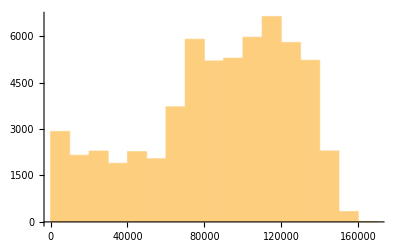

```mathematica
datafull=Join[Partition[Range@60000,1],Partition[Flatten@Table[ConstantArray[i,300],{i,200}],1],Partition[Flatten[objfuncsforsequences[[All,3]],1],1],2];
Histogram@datafull[[All,3]]
```

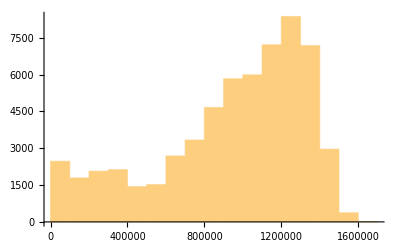

```mathematica
datafull2=Join[Partition[Range@60000,1],Partition[Flatten@Table[ConstantArray[i,300],{i,200}],1],Partition[Flatten[objfuncsforsequenceswider[[All,3]],1],1],2];
Histogram@datafull2[[All,3]]
```

```mathematica
x2=Round@Ceiling[Length@datafull/19,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t},2,1]}],1]];
win2=Length@data2;
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,3,2500,win2];]
```

{11.691,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
graphsandnodenumbers12[[All,2]]
```

{41,35,40,47,55,58,59,50,54,57,52,50,53,60,53,50,57,48,37,47,49,44,48,50,51,54,48,49,51,46,43,48,48,46,49,47,51}

```mathematica
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{479.992,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{41,35,40,47,55,58,59,50,54,57,52,50,53,60,53,50,57,48,37,47,49,44,48,50,51,54,48,49,51,46,43,48,48,46,49,47,51}

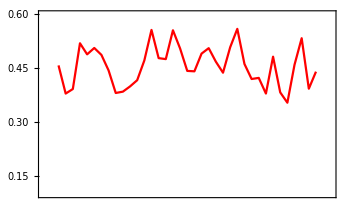
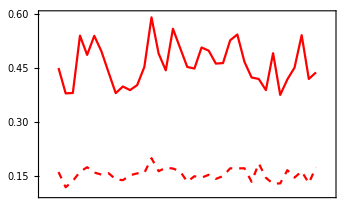
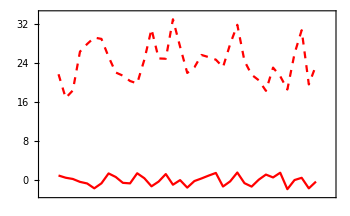

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.6};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,3,bucketnode12,win2];]
```

{2.5902,Null}

```mathematica
bucketsize32=Flatten@widthdataintimewindowsFixedbucket2[[4]]
```

{78,91,79,68,58,55,54,64,59,56,61,64,60,53,60,64,56,66,86,68,65,72,66,64,62,59,66,65,62,69,74,66,66,69,65,68,62}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{495.024,Null}

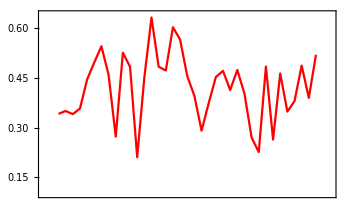
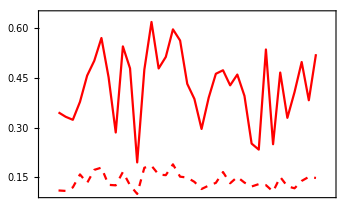
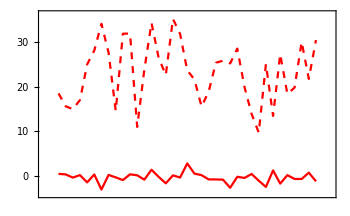

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

wider objective coefficients

```mathematica
x2=Round@Ceiling[Length@datafull2/19,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t}=Join[Range[x2,Length@datafull2,x2],{Length@datafull2}];
data2=Join[{Take[datafull2,{1,a}]},Flatten[Table[{Take[datafull2,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull2,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t},2,1]}],1]];
win2=Length@data2;
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,3,25000,win2];]
```

{11.0224,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
graphsandnodenumbers12[[All,2]]
```

{54,46,47,51,46,55,56,56,54,44,35,36,45,47,45,52,53,51,44,48,49,41,42,42,47,49,45,48,43,46,52,53,56,47,48,49,52}

```mathematica
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{1602.38,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{54,46,47,51,46,55,56,56,54,44,35,36,45,47,45,52,53,51,44,48,49,41,42,42,47,49,45,48,43,46,52,53,56,47,48,49,52}

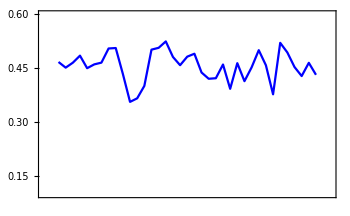
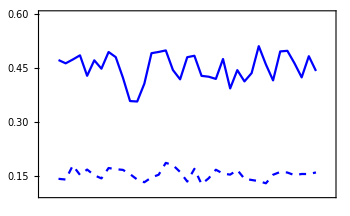
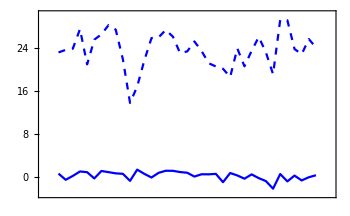

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.6};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Blue,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Blue]}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Blue]}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,3,bucketnode12,win2];]
```

{8.88334,Null}

```mathematica
bucketsize32=Flatten@widthdataintimewindowsFixedbucket2[[4]]
```

{59,69,68,62,69,58,57,57,59,72,91,88,71,68,71,61,60,62,72,66,65,78,76,76,68,65,71,66,74,69,61,60,57,68,66,65,61}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{542.518,Null}

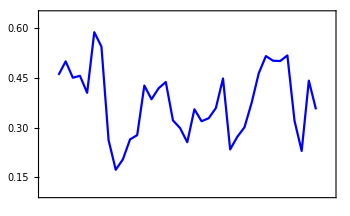
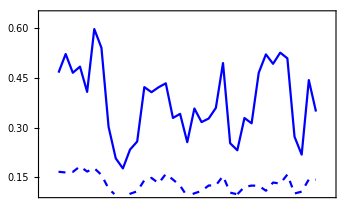
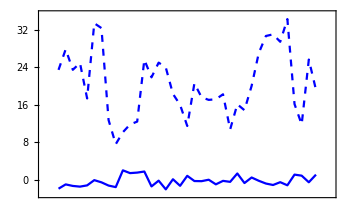

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Blue,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Blue]}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Blue]}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```